# Boolean Algebra *will change it to sth more interesting*

Dali Lai

1. Combinational Circuit-logic gate

By combining different logic gates (AND, NAND, OR...etc.), the circuit can output the desired output while receiving a certain input. 
In programming, know as truth table (but more complicated). 

For example X or Y:

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[x||y,{x},{y}],{"1","0"}],{"x/y","1","0"}}],Frame->All]
```

x/y | 1 | 0
1 | True | True
0 | True | False

```mathematica
(*I kinda hard coded the 1 and 0, any other way to do it ? Like how to make is count as binary from 00 to w/e many the cell there is ? i.e. 4 cells then it will be 00 01 10 11*)
```

To prove it, let’s simulate the logic gate OR with 2 inputs in SystemModeler 

-Graphics-

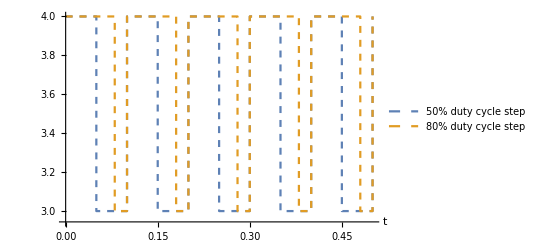

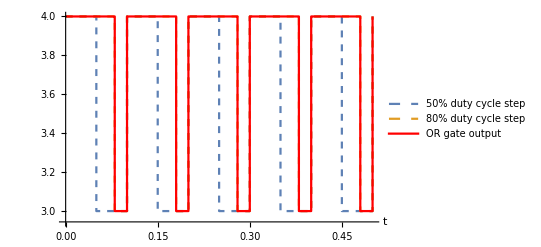

```mathematica
orgate=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step","80% duty cycle step"},PlotStyle->Thick]
Show[orgate,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"orGate1.y"},PlotLegends->{"OR gate output"},PlotStyle->{Red,Thin}]]
```

Another example for XOR gate:

-Graphics-

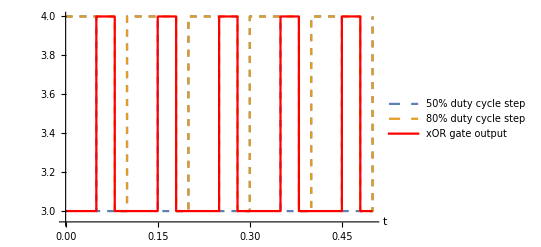

```mathematica
xorgate=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step","80% duty cycle step"},PlotStyle->Thick]
Show[xorgate,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"xorGate1.y"},PlotLegends->{"xOR gate output"},PlotStyle->{Red,Thin}]]
```

2. Combinational Circuit-logic expression

As the tittle indicated, this is about the combination of logic gates, and its application.  
Here are some examples about the combinational circuit examples that are more than 2 inputs and hard to see the result just by hand.
Lets say a 4 inputs combinational circuit:

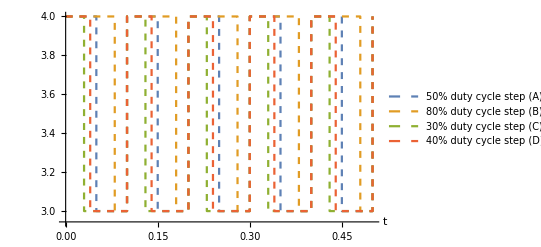

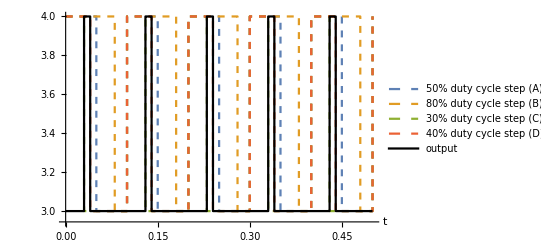

```mathematica
gate4=SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"pulse1.y","pulse2.y","pulse3.y","pulse4.y"},PlotStyle->Dashed,PlotLegends->{"50% duty cycle step (A)","80% duty cycle step (B)","30% duty cycle step (C)","40% duty cycle step (D)"},PlotStyle->Thick]
Show[gate4,SystemModelPlot[SystemModelSimulate[-Graphics-,{0,0.5}],{"xorGate1.y"},PlotLegends->{"output"},PlotStyle->{Black,Thin}]]
```

Notice that these kind of combinational circuit are a bit hard to know the truth table just from head directly, but still can be written the whole expression by hand (and will always be)
By writing the whole expression by hand, one can get the output logic expression is equal to 
((A∨B∨C)⊼(C))⊻(C⊽D)
And... it’s still not very clear what the output is.

```mathematica
BooleanMinimize[((A∨B∨C)⊼(C))⊻(C⊽D)]
```

!C&&D

The whole logic expression, most of the time, can be simplified using different axioms of switching algebra , Demorgan’s law...etc. 
Just check some truth table to make sure they are the same thing.

```mathematica
Grid[MapThread[Prepend,{Prepend[BooleanTable[((A∨B∨CC)⊼(CC))⊻(CC⊽DD),{A,B},{CC,DD}],{"11","10","01","00"}],{"AB/CD","11","10","01","00"}}],Frame->All]
```

AB/CD | 11 | 10 | 01 | 00
11 | False | False | True | False
10 | False | False | True | False
01 | False | False | True | False
00 | False | False | True | False

```mathematica
BooleanTable[!C&&D,{C,D}]//TraditionalForm
```

{False,False,True,False}

Can confirm that the output of this logic circuit won’t depends on A and B at least in simulation and most of the time.